### Preamble

```mathematica
ClearGlobal[];
```

```mathematica
$Assumptions={ {Lx, Ly, Lz}∈Reals, Lx>0, Ly>0, Lz>0, L>0, Ixx>0};
SetDirectory[NotebookDirectory[]];
Needs["Calc3DMatProp`"]
```

### Geometry and topology definition

```mathematica
nodes={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,0,1},{0,1,1},{1,1,0},{1,1,1},{1/2,1/2,1/2},{1/2,0,1/2},{0,1/2,1/2},{1/2,1,1/2},{1,1/2,1/2},{1/2,1/2,0},{1/2,1/2,1}}L;
beams={{3,1},{1,2},{2,7},{7,3},{4,5},{5,8},{8,6},{6,4},{1,4},{2,5},{7,8},{3,6}};
shells={{10,1,2},{10,2,5},{10,5,4},{10,4,1},{11,1,3},{11,3,6},{11,6,4},{11,4,1},{12,3,6},{12,6,8},{12,8,7},{12,7,3},{13,7,8},{13,8,5},{13,5,2},{13,2,7},{14,1,2},{14,2,7},{14,7,3},{14,3,1},{15,4,5},{15,5,8},{15,8,6},{15,6,4}};
nnodes=Dimensions[nodes]⟦1⟧;
nbeams=Dimensions[beams]⟦1⟧;
a1=nodes⟦2⟧-nodes⟦1⟧;a2=nodes⟦3⟧-nodes⟦1⟧;a3=nodes⟦4⟧-nodes⟦1⟧;
V=a1.a2×a3;
{αs,βs,γs}={(Es (ν-1))/(2 ν^2+ν-1),-(Es ν)/(2 ν^2+ν-1),Es/(2 ν+2)};
```

```mathematica
Eqs={{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1}};
(* Eqs={{1,1,1,1,1,1,1,1,0}};*)
{B0,Bϵ}=MakeB0andBe[Eqs,nodes]//Simplify;
```

```mathematica
rbeams={{3},{4},{5},{6},{7},{8},{10},{11},{12}};
rshells={{9},{10},{11},{12},{13},{14},{15},{16},{21},{22},{23},{24}};
```

```mathematica
ρ=CalcModelVolume[nodes, Delete[beams,rbeams],Delete[shells,rshells],  {A, 2 Iyy, Iyy, Iyy},{Es,ν,t}]/V//Simplify;
```

```mathematica
Graph1=DrawUnitCell[nodes/.{ L->1}, beams,shells]
Graph2=DrawUnitCell[nodes/.{ L->1},  Delete[beams,rbeams],Delete[shells,rshells]]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* Export["cubicCell.eps",Rasterize[Graph1, ImageResolution->600,Background->None]]
Export["cubicCellPrim.eps",Rasterize[Graph2, ImageResolution->600,Background->None]] *)
```

## Find material stiffness matrix

### Only beams

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2 Iyy, Iyy, Iyy},{Es,ν,t},{1,0,0}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L^2/(A Es)Kmat/.{Iyy->0}//Simplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
L^4/(Es Iyy)Kmat/.{ A->0}//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0
0 | 0 | 0 | 0 | 6 | 0
0 | 0 | 0 | 0 | 0 | 6)

### Only shells

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{0,1,0}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L/(Es t) Kmat//Simplify
```

{{-2/(-1+ν^2),ν/(1-ν^2),ν/(1-ν^2),0,0,0},{ν/(1-ν^2),-2/(-1+ν^2),ν/(1-ν^2),0,0,0},{ν/(1-ν^2),ν/(1-ν^2),-2/(-1+ν^2),0,0,0},{0,0,0,1/(2+2 ν),0,0},{0,0,0,0,1/(2+2 ν),0},{0,0,0,0,0,1/(2+2 ν)}}

### Only plates

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{0,0,1}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L^3/(Es t^3)Kmat//Simplify
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,-(8 (-153+48 ν+4 ν^2))/(27 (-7+2 ν) (-1+ν^2)),0,0},{0,0,0,0,-(8 (-153+48 ν+4 ν^2))/(27 (-7+2 ν) (-1+ν^2)),0},{0,0,0,0,0,-(8 (-153+48 ν+4 ν^2))/(27 (-7+2 ν) (-1+ν^2))}}

### Everything

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{1,1,1}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
```

```mathematica
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
{α, β, γ}={Kmat[[1,1]], Kmat[[1,2]], Kmat[[6,6]]};
BeamForces=Table[GetBeamForces[kk,dϵ.{1,0,0,0,0,0}, nodes,beams,{Es,Es/(2(1+ν))},{A, 2 Iyy, Iyy, Iyy}], {kk,1,nbeams}];
```

### Some plots

```mathematica
{α,β,γ}={Kmat⟦1,1⟧,Kmat⟦1,2⟧,Kmat⟦6,6⟧};
```

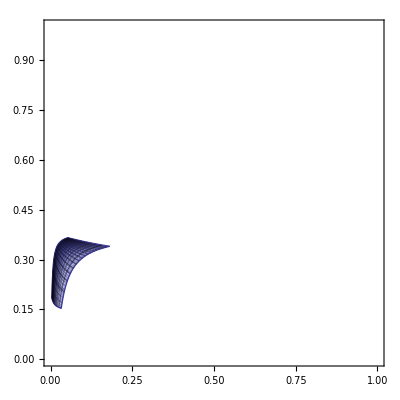

```mathematica
ParametricPlot[Simplify[Evaluate[{ρ,(α+2 β)/((αs+2 βs)ρ)}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},PlotRange->{{0,1},{0,1}},AspectRatio->Full]
```

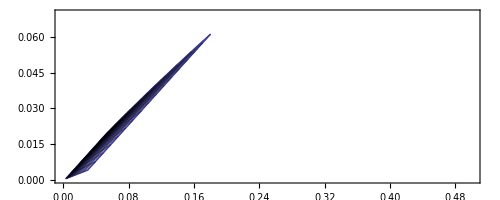

```mathematica
ParametricPlot[Simplify[Evaluate[{ρ,(α+2 β)/(αs+2 βs)}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},PlotRange->{{0,0.5},{0,0.07}},AspectRatio->Full]
```

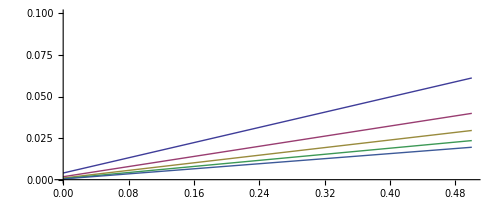

```mathematica
Plot[Evaluate[Table[Simplify[(α+2 β)/(αs+2 βs)/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,0.5},PlotRange->{{0,0.5},{0,0.1}},AspectRatio->Full]
```

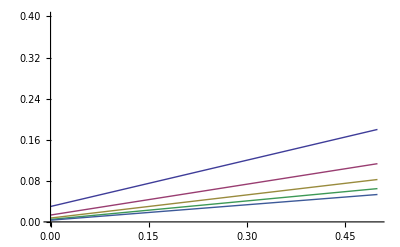

```mathematica
Plot[Evaluate[Table[Simplify[ρ/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,.5}, PlotRange->{0, 0.4}]
```

### Element stresses

```mathematica
Cmat=Inverse[Kmat]//Simplify;
```

```mathematica
BeamForces=Simplify[Table[GetBeamForces[kk,dϵ.Cmat.{0,0,0,1,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}],{kk,1,nbeams}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}];
```

```mathematica
BeamForces
```

```mathematica
BeamForces[[1,2,2]]
```

```mathematica
N1=Simplify[GetBeamForces[2,dϵ.Cmat.{1,1,1,0,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}][[1,1]];
M1=0;
```

```mathematica
N2=Simplify[GetBeamForces[2,dϵ.Cmat.{1,0,-1,0,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}][[1,1]];
M2=0;
```

```mathematica
N3=0;
M3=Simplify[GetBeamForces[1,dϵ.Cmat.{0,0,0,1,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}][[2,2]];
```

```mathematica
ParametricPlot[Simplify[Evaluate[{{ρ,N1/A},{ρ,N2/A},{ρ,N3/A}}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},AspectRatio->Full]
```

```mathematica
ParametricPlot[Simplify[Evaluate[{{ρ,M1/(d A)},{ρ,M2/(d A)},{ρ,M3/(d A)}}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},AspectRatio->Full]
```

```mathematica
Plot[Evaluate[Table[Simplify[N1/A/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,.5}]
```